```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
h[n_,ρ_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,2,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
(* periodic bc *)
PrependTo[tblw,{1,1+F0}->ρ];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* choose system size *)
n=12;
L=Fibonacci[n+2];
(* choose coupling *)
ρ=.5;
(* compute eigenstates and eigenvalues *)
{val,vec}=Eigensystem[h[n,ρ]];
(* order both by increasing energy *)
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];
```

```mathematica
L
```

377

```mathematica
L/2.
```

188.5

```mathematica
(* choose a site *)
r =188;
(* collect wavevector coefficients at this site *)
ψr=Transpose[vec][[r]];
(* intensity *)
intr=Abs[ψr]^2;
(* compute the time-dependant part of the return autocorrelation function *)
corr[t_]:=2 Sum[intr[[a]]intr[[b]]Sinc[(val[[a]]-val[[b]])t],{a,L},{b,a}]
(* construct a time range *)
tRange=10^(Range[0,3,.03]);
(* evaluate the autocorrelation over it *)
corrT16=ParallelMap[corr,tRange];
```

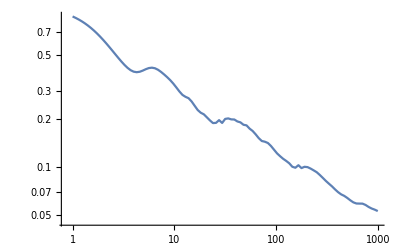

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
corrT3=glue[tRange,corrT16];
Export[NotebookDirectory[]<>"data/spreading_autocorrelation_rho05_n14.dat",%];
ListLogLogPlot[corrT3,PlotRange->All,Joined->True]
```

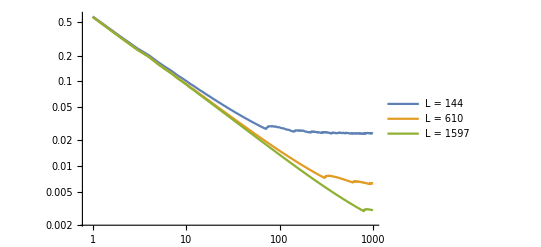

```mathematica
(* plot the result *)
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
corrT1=glue[tRange,corrT];
corrT2=glue[tRange,corrT13];
corrT3=glue[tRange,corrT15];
ListLogLogPlot[{corrT1,corrT2,corrT3},PlotRange->All,Joined->True,PlotLegends->("L = "<>ToString[#]&/@{144,610,1597})]
```

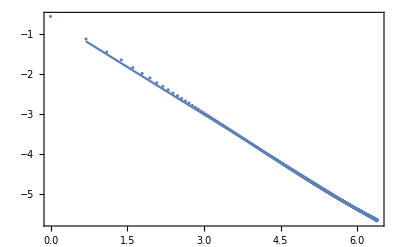

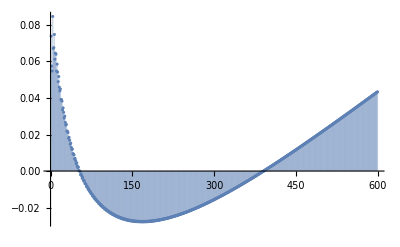

```mathematica
tmin=2;
tmax=600;
TcorrT3=corrT15-corrT15[[1]];
dat=Log[corrT3[[tmin;;tmax]]];
fit=LinearModelFit[dat,tt,tt];
Show[ListPlot[dat],Plot[fit[tt],{tt,Log[tmin],Log[tmax]}],Frame->True,PlotRange->All]
ListPlot[fit["FitResiduals"], Filling->Axis]
```

```mathematica
fit
```

FittedModel[-0.498678-0.824888 tt]

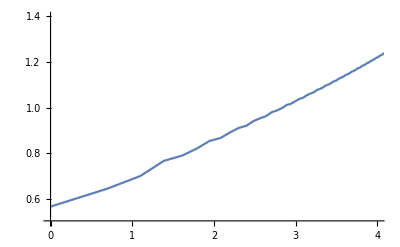

```mathematica
(* plot the result *)
TcorrT3=corrT15;
TcorrT3=glue[Log[tRange],tRange*TcorrT3];
ListPlot[TcorrT3,Joined->True,PlotRange->{{0,4},{0.5,1.4}}]
```

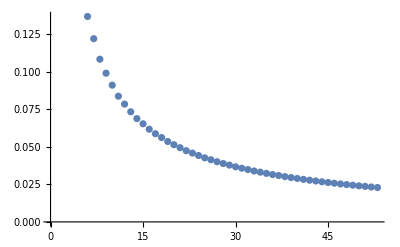

```mathematica
ListPlot[dat]
```

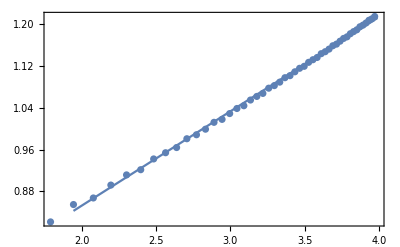

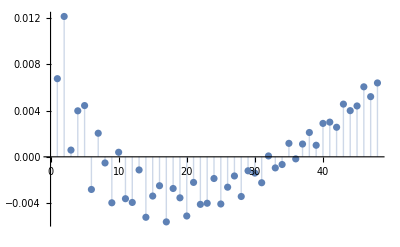

FittedModel[0.491035+0.180706 tt]

```mathematica
tmin=Floor@Exp[2];
tmax=Floor@Exp[4];
TcorrT3=corrT15;
TcorrT3=glue[Log[tRange],tRange*TcorrT3];
dat=TcorrT3[[tmin;;tmax]];
fit=LinearModelFit[dat,tt,tt];
Show[ListPlot[dat],Plot[fit[tt],{tt,Log[tmin],Log[tmax]}],Frame->True,PlotRange->All]
ListPlot[fit["FitResiduals"], Filling->Axis]
fit
```